```mathematica
Clear["Global`*"]
```

```mathematica
scaling=1;
a=scaling N[14/10];   (* == Carbon-Carbon Distance in A == *)
a0=√3 a ;(* == Lattice Constant Graphene == *) (*WARNING: With this definition a0!=2.46, a0=2.42487*)

(* == Direct Lattice == *)
a2=a0{1,0};  a1=a0{1/2,(√3)/2};                           (* == Direct Lattice Vectors. Defined as to match convention in the trilayer article == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);                             (* == High symmetry points == *)
kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);

(* == Reciprocal Lattice == *)

{b1,b2}=2 π Inverse[Transpose[{a1,a2}]];  (* == Reciprocal Lattice Vectors == *)

b3=-( b1+b2);  
kg={0,0}; kp=1/3*(2 b1+b2);                             (* == High symmetry points == *)
km=1/2(b1+b2);  kk=1/3(b1+2 b2);


n=3600;(*Nk=3 n^2*) (* n = number of points that the mesh of the full 1BZ (with same Δk distance) would have*)
δn=120; (* δn = parameter analogous to n, but for the mini-kmesh*)
Nq=2n; (*Nq = is the number of q points for which Π(q) will be calculated*)
{iqf,jqf}={0,n}; (*The indices of the vector pointing to the end of the q-path*)


Npockets=2;
Vpocket=Table[0.,{i,1,Npockets}];
(*Defining where each pocket is centered at:*)
Vpocket[[1]]=-kp;
Vpocket[[2]]=-kk;

(*This function transltes from indices i,j to vectors: *)
IndexToVector[kij_,k0_]:=Module[{sol},
sol=Table[kij[[i,j]].(1/n{kk,kp})+k0,{i,1,Length[kij]},{j,1,Length[kij[[i]]]}]
];
(*Defining k mesh, first with indices, then with vectors:*)
k0ij=Module[{sol},
sol=Table[{i,j},{i,-δn+1,δn},{j,Max[-δn,-δn-i]+1,Min[δn,δn-i]}]
];
k0pmesh=Table[IndexToVector[k0ij,Vpocket[[i]]],{i,1,Npockets}];
(*Defining the k+q*)
kqpathpij=Module[{sol},
sol=Table[{i,j},{i,-δn+1,δn},{j,Max[-δn,-δn-i]+1-jqf,Min[δn,δn-i]+jqf}]
];
kqpathpmesh=Table[IndexToVector[kqpathpij,Vpocket[[i]]],{i,1,Npockets}];

(*The following mesh serves to ilustrate how a set of points from the kq mesh are taken along the path*)
iq=0.5 Nq;
kqij=Apply[kqpathpij[[#1+δn,#2+iq-Max[-δn,-δn-#1]]] &,k0ij,{2}];

kqpmesh=Table[IndexToVector[kqij,Vpocket[[i]]],{i,1,Npockets}];
```

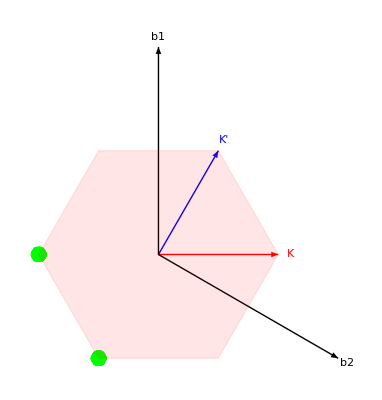

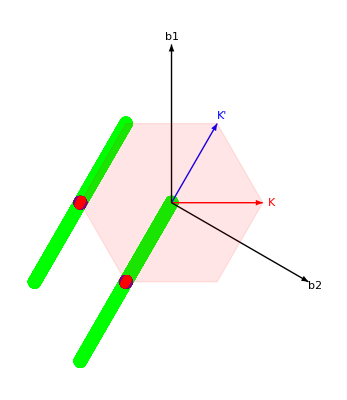

```mathematica
(*Only run for visualization at small n, otherwise takes too much RAM*)
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a0))*{-1,0},((4π)/(3a0))*{(-1)/2,(√3)/2},((4π)/(3a0))*{1/2,(√3)/2},((4π)/(3a0))*{1,0},((4π)/(3a0))*{1/2,(-√3)/2},((4π)/(3a0))*{(-1)/2,(-√3)/2}}];
ps=0.015;
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.1],EdgeForm [Dashed],
BZcontour
}];
(*Plotting the k mesh: *)
Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[k0pmesh[[i]],1]],{i,1,Npockets}]}],
BZvectors
]

ii=0;
Show[
Graphics[{
PointSize[ps],
Green,
Table[Point[Flatten[kqpathpmesh[[i]],1]],{i,1,Npockets}],
Purple,
Table[Point[Flatten[kqpmesh[[i]],1]],{i,1,Npockets}]
,
Red,
Table[
Point[Table[kqpathpmesh[[ip]][[ii+δn,i-Max[-δn,-δn-ii]]],{i,iq-δn+1,iq+δn}]]
,{ip,1,Npockets}]
}],
BZvectors
]
```

```mathematica
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a0]*Exp[-ⅈ*ky*a0*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a0*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]]; 
(*Thermodynamic quantities*)
μ=-0.052175;(* VHS is at μ=-0.052175;*)
kbT=0.0000861*1; (*Boltzmann's k × temperature*)
δc=10.*kbT; (*cutoff for the Fermi-Dirac distribution*)
FDif[ϵk_]=If[Abs[μ-ϵk]<δc,1/(1+Exp[(ϵk-μ)/kbT]),UnitStep[μ-ϵk]];
δFif[ϵk_]=If[Abs[μ-ϵk]<δc,-1./kbT/(2*(1+Cosh[(ϵk-μ)/kbT])),0.];
```

```mathematica
(*Diagonalizing H at the points of the kq mesh*)
(*These arrays hold the same {i,j} structure than kij*)
Ekqpathpij=Table[Map[Eigenvalues,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
ψkqpathpij=Table[Map[Eigenvectors,Apply[Hk,kqpathpmesh[[i]],{2}],{2}],{i,1,Npockets}];
nfEkqpathpij=Table[Map[FDif[#]&,Ekqpathpij[[i]],{3}],{i,1,Npockets}];
(*Defining which points correspond to the k mesh*)
i0=n;
Ek=Flatten[Table[Flatten[Apply[Ekqpathpij[[i]][[#1+δn,#2+i0-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
ψk=Flatten[Table[Flatten[Apply[ψkqpathpij[[i]][[#1+δn,#2+i0-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
nfEk=Flatten[Table[Flatten[Apply[nfEkqpathpij[[i]][[#1+δn,#2+i0-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{i,1,Npockets}],1];
```

```mathematica
(*Only run for visualization at small n, otherwise takes too much RAM*)
i=0;
(*iq=1.Nq;*)
Epath[iqq_]:=Table[
Flatten[Table[{(ii+iqq+δn) Norm[kk/n],Ekqpathpij[[ip]][[i+(n-λ),ii+iqq-Max[-(n-λ),-(n-λ)-i]]][[j]]},{ii,-δn+1, δn},{j,Nb}],1]
,{ip,1,Npockets}];

K0=Norm[kk/n] Nq ;
δK=3.Norm[kk];
δE=3.5 γ0;
Manipulate[
ListPlot[Epath[Floor[iq Nq]],PlotRange->{{K0-δK,K0+δK},{-δE,δE}}]
,{iq,0,1}]
```

```mathematica
Nq0=12; (*Number of q points to be sampled in the first run*)
qstep=Nq/Nq0(*size of q-steps in units of Δk spacings in the first sampling run*)
Lq=2 Norm[kk]; (*For the case of K-Γ-K' path*)
Δq=Lq/Nq;
ω=0.;
```

600

Πq0={{0,0.0925813},{600,0.00408289},{1200,0.00295963},{1800,0.00292843},{2400,0.00363586},{3000,0.00621477},{3600,0.259112},{4200,0.00616975},{4800,0.00361925},{5400,0.00292387},{6000,0.00296215},{6600,0.00409228},{7200,0.0925878}}

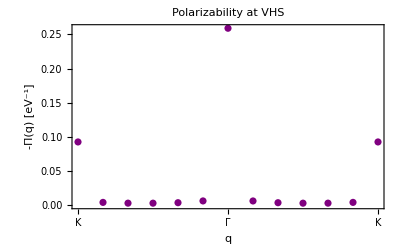

```mathematica
Πq0=Table[{0.,0.},{i,1,Nq0+1}];
Monitor[

Table[

iProgressIndicator=i  ;  (*Used for progress bar only*)

Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+δn,#2+i qstep-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+δn,#2+i qstep-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+δn,#2+i qstep-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];

Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];

ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;

ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];

Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];


idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;

Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq0[[i+1,1]]=i qstep;
Πq0[[i+1,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq]
,{i,0,Nq/qstep}]
,
ProgressIndicator[iProgressIndicator,{0,1.05 Nq0}]
];
StringForm["Πq0=``",Πq0]
Show[ListPlot[Πq0, PlotRange-> All,PlotStyle-> Purple,Joined->False,Frame-> True, FrameLabel->{"q",-"Π(q) [eV^-1]"},FrameTicks->{{Automatic,None},{{{0,"K"},{n,"Γ"},{2n,"K"}},None}},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

{27,3514,3552,3571,3609,3627,3646,3684,3702,7171}

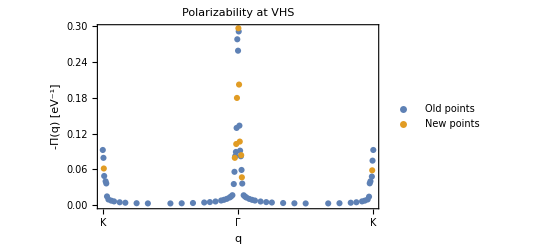

Old points: …

New points: {{27,0.0615265},{3514,0.0794183},{3552,0.1026},{3571,0.179887},{3609,0.296775},{3627,0.202296},{3646,0.106675},{3684,0.0838562},{3702,0.0466992},{7171,0.0584653}}

Full set: …

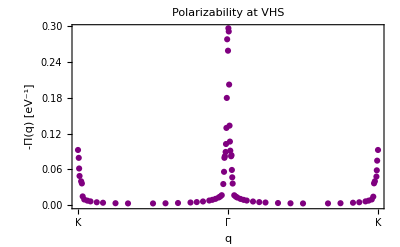

```mathematica
(*Adaptive sampling in q*)
(*Here we calculate more points for the Π plot, choosing to calculate for values of q where Π changes the most*)
(*In this cell, the distance between neighboring points in Πq0 is measured.
Then we pick the the first NiMax points with the largest distance to their neighbors, and calculate Πq0 in between those points.*)
Πq0=DeleteDuplicates[Πq0];
DΠ=Table[{Πq0[[i,1]],(Abs[Πq0[[i+1,2]]-Πq0[[i,2]]]+0.0001)^-1},{i,1,Length[Πq0]-1}];
NiMax=10;(*Must be smaller than initial number of points!*)
qstep=0.5 qstep;
iDmaxOrigi=Floor[Sort[DΠ[[Ordering[DΠ[[All,2]]],1]][[1;;NiMax]]]+qstep]
Πq02=Table[{0.,0.},{i,1,NiMax}];
Monitor[
Table[
iProgressIndicator=i  ;  (*Used for progress bar only*)
Ekq=Flatten[Table[Flatten[Apply[Ekqpathpij[[ip]][[#1+δn,#2+iDmaxOrigi[[i]] -Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
ψkq=Flatten[Table[Flatten[Apply[ψkqpathpij[[ip]][[#1+δn,#2+iDmaxOrigi[[i]]-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
nfEkq=Flatten[Table[Flatten[Apply[nfEkqpathpij[[ip]][[#1+δn,#2+iDmaxOrigi[[i]]-Max[-δn,-δn-#1]]] &,k0ij,{2}],1],{ip,1,Npockets}],1];
Δnf=Flatten[Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Length[nfEk]}]];
ΔE=Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]]-Tuples[{Ek[[i]],Ekq[[i]]}][[All,2]],{i,Length[Ek]}]]+ω;
ψTuples=Table[Tuples[{ψk[[i]],ψkq[[i]]*}],{i,Length[Ek]}];
Fkq=Flatten[Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Length[Ek]},{j,Nb^2}]];
idiv=Flatten[Position[Abs[ΔE],_?(#==0.&)]];
ΔE[[idiv]]=1.;
Δnf[[idiv]]=Map[δFif[#]&,Flatten[Table[Tuples[{Ek[[i]],Ekq[[i]]}][[All,1]],{i,Length[Ek]}]][[idiv]]];
Πq02[[i,1]]=iDmaxOrigi[[i]];
Πq02[[i,2]]=-(2/(3 n^2))*Total[Δnf*Re[1/ΔE]*Fkq],
{i,1,NiMax}],
ProgressIndicator[iProgressIndicator,{0,1.05 Nq0}]
];
Show[ListPlot[{Πq0,Πq02},PlotRange->All,Frame-> True,Axes->False, FrameLabel->{"q",-"Π(q) [eV^-1]"},
FrameTicks->{{Automatic,None},{{{0,"K"},{n,"Γ"},{2n,"K"}},None}},
LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"],PlotLegends->{"Old points", "New points"}]]
Π1p2=Join[Πq0,Πq02];
Ordering[Π1p2[[All,1]]];
StringForm["Old points: ``",Πq0]
StringForm["New points: ``",Πq02]
Πq0=Π1p2[[Ordering[Π1p2[[All,1]]]]];
StringForm["Full set: ``",Πq0]
Show[ListPlot[Πq0, PlotRange-> All,PlotStyle-> Purple,Joined->False,Frame-> True,
FrameTicks->{{Automatic,None},{{{0,"K"},{n,"Γ"},{2n,"K"}},None}},Axes->False, FrameLabel->{"q",-"Π(q) [eV^-1]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Polarizability at VHS"]]]
```

```mathematica
(*Parameters for Vscr*)
CouConst=8.987 10^9;
eCharge=1.602 10^-19;
ϵ=4.;
ω0=17.;
V=(eCharge^2 CouConst/(a0 10^-10 ϵ)) 6.241 10^18;
V0=ω0/ϵ;

nR=700;
(*This function transltes from indices i,j to vectors: *)
IndexToVectorR[Rij_]:=Module[{sol},
sol=Table[Rij[[i,j]].({a1,a2}/a0 ),{i,1,Length[Rij]},{j,1,Length[Rij[[i]]]}]
];

(*kij the indices of the vectors in the k-mesh: *)
R0ij=Module[{sol},
sol=Table[{N[i],N[j]},{i,-nR,nR},{j,Max[-nR,-nR-i],Min[nR,nR-i]}]
];
R0ij= Delete[R0ij,Position[R0ij,{0.,0.}]];
R0ijmesh=IndexToVectorR[R0ij];
R0=Flatten[R0ij,1];
R0mesh=Flatten[R0ijmesh,1];
VC[qxa0_,qya0_]:=V0+V  Total[Exp[-ⅈ R0mesh.{qxa0,qya0}]/Map[Norm,R0mesh]];
```

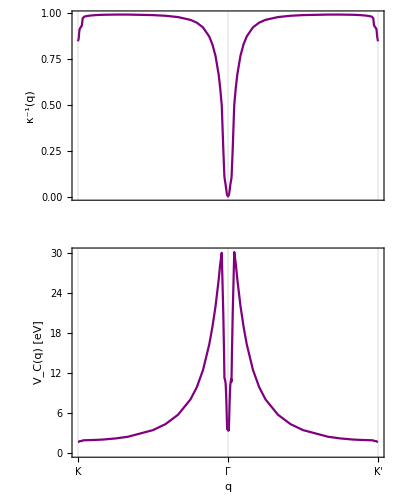

```mathematica
(*Calculation of Vscr and κ^-1*)
Lq=2 Norm[kk];
Δq=Lq/Nq;
qi= Table[-kp+Πq0[[i,1]]/Nq(kp+kp),{i,1,Length[Πq0]}];
Πq0q=Table[{Πq0[[i,1]],qi[[i]],Πq0[[i,2]]},{i,1,Length[Πq0]}];
Π=Πq0q[[All,3]];
qia0=a0 Πq0q[[All,2]];
iq=Πq0q[[All,1]];
Vcq=Apply[VC,qia0,{1}];
Vscr=Vcq/(1+Vcq Π);
VscrKpM=Transpose[{iq,Vscr}];
κKpM=Transpose[{iq,Vscr/Vcq}];

Figκ=ListPlot[κKpM, PlotRange-> All,PlotStyle-> Purple,Joined-> True,Frame-> True,FrameTicks->{{Automatic,None},{None,None}}, FrameLabel->{None,"κ^-1(q)"},LabelStyle->Directive[Black,15,FontFamily->"Times"],GridLines->{{0,n,2n},None}];
FigVscr=ListPlot[VscrKpM, PlotRange-> All,PlotStyle-> Purple,Joined->True,Frame-> True,Axes->False, FrameLabel->{"q","V_C(q) [eV]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],FrameTicks->{{Automatic,None},{{{0,"K"},{n,"Γ"},{2n,"K'"}},None}},GridLines->{Automatic,None}];

GraphicsColumn[{Figκ,FigVscr}]
```